```mathematica
Animate[
ContourPlot[-12 w^2+4 x w+x^2+5 y w+2x y+2 y^2==0,{x,-10,10},{y,-10,10}],{w,-1,1,1}]
```

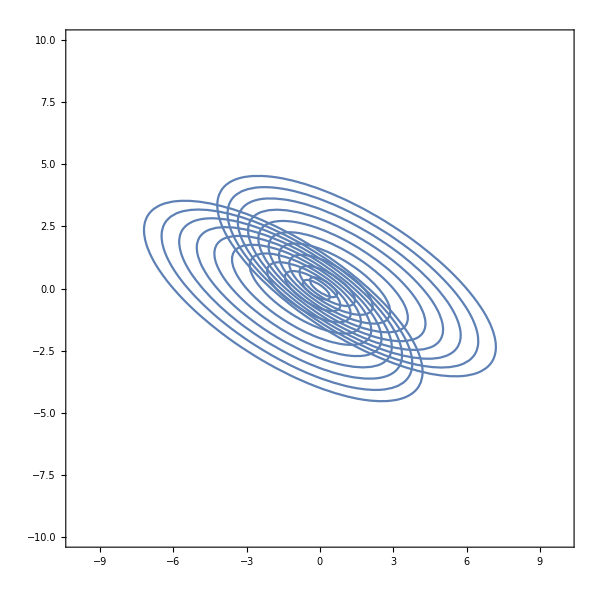

```mathematica
Show[Table[
ContourPlot[-12 w^2+4 x w+x^2+5 y w+2x y+2 y^2==0,{x,-10,10},{y,-10,10}],{w,-1,1,0.1}]]
```

```mathematica
ContourPlot3D[{-12 w^2+4 x w+x^2+5 y w+2x y+2 y^2==0,(-6)x+0+2*(-6y)/2+4*(x-6w)/2+5 y/2-12w==0,
(4)x+2(-4)y+2*(4y-4x)/2+4*(x+4w)/2+5(y-4w)/2-12w==0,
(1)x+2(-8)y+2*(y-8x)/2+4*(x+w)/2+5(y-8w)/2-12w==0},{x,-10,10},{y,-10,10},{w,-1,1}]
```

-Graphics3D-

```mathematica
-12+4 x +x^2+5 y +2x y+2 y^2==0
```

-12+4 x+x^2+5 y+2 x y+2 y^2==0

```mathematica
FindInstance[-12+4 x+x^2+5 y+2 x y+2 y^2==0,{x,y},Integers,3]
```

{{x→4,y→-4},{x→-7,y→3},{x→3,y→-1}}

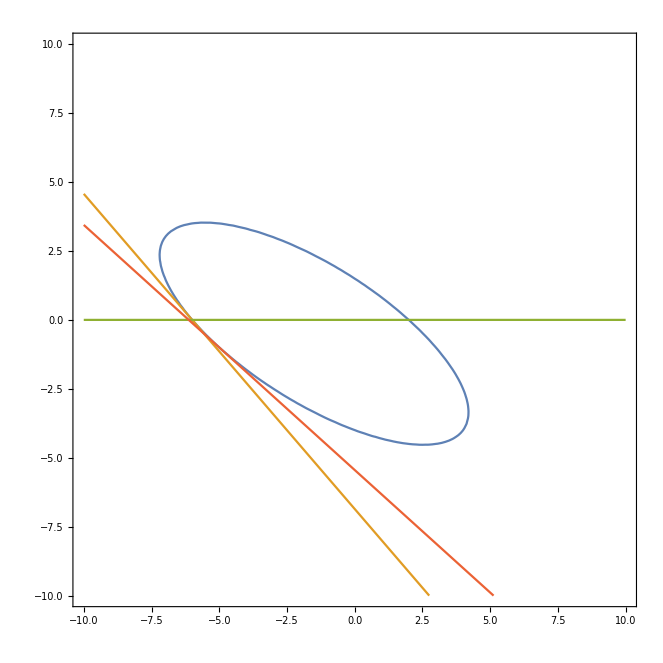

```mathematica
ContourPlot[{x^2+2 y^2+2x y+4x+5y-12==0,
(-6)x+0+2*(-6y)/2+4*(x-6)/2+5 y/2-12==0,
y==0,(-5)x+2(-1)y+2*(-5y-x)/2+4*(x-5)/2+5(y-1)/2-12==0,},{x,-10,10},{y,-10,10}]
```

```mathematica
Solve[{(-6)x+0+2*(-6y)/2+4*(x-6w)/2+5 y/2-12w==0,
(4)x+2(-4)y+2*(4y-4x)/2+4*(x+4w)/2+5(y-4w)/2-12w==0,w==1},{x,y,w}]
```

{{x→1,y→-8,w→1}}

```mathematica
ContourPlot3D[{-12 w^2+4 x w+x^2+5 y w+2x y-2 y^2==0，w==0},{x,-10,10},{y,-10,10},{w,-1,1}]
```

```mathematica
ContourPlot3D[{-12 w^2+4 x w+x^2+5 y w+2 x y-2 y^2==0, w==0},{x,-10,10},{y,-10,10},{w,-1,1}]
```

-Graphics3D-

```mathematica
ContourPlot3D[{-12 w^2+4 x w+x^2+5 y w+2 x y+ y^2==0, w==0},{x,-10,10},{y,-10,10},{w,-1,1}]
```

-Graphics3D-